# Saha equation and potential lowering

## ionization order z

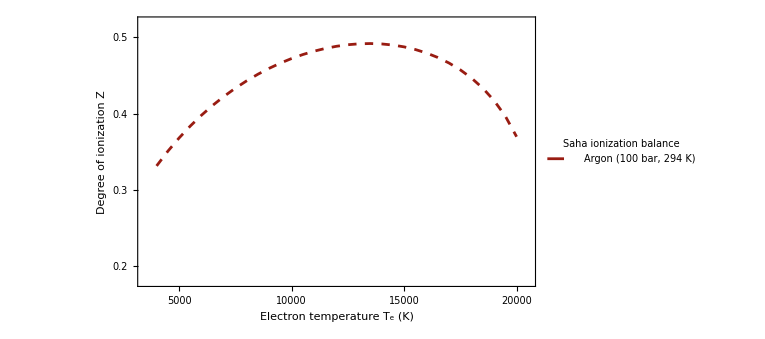

```mathematica
(* -- z function -- *)
Clear[z];
zFunc[T_:11000,zini_:.6]:=Block[{ϵ0,ℏ,n0,ne,e,kB,me,χ1,Q0,Qi,Δχ,zlowering,sol},

(* -- constants -- *)
ϵ0=8.854*^-12;
ℏ=1.055*^-34;
n0=2.6*^27;
ne=z n0;
e=1.6*^-19;
kB=1.38*^-23;
me=9.109*^-31;

(* -- ionization potential -- *)
χ1=15.8 e;
Q0=1.00; (* partition function of Ar I from NIST *)
Qi=5.66; (* partition function of Ar II from NIST *)
Δχ=((z+1)e^2)/(4π ϵ0)√((z(z+1) n0 e^2)/(ϵ0 kB T))*(1/e);
zlowering=2/n0 Qi/Q0((me kB T)/(2π ℏ^2))^(3/2)Exp[-(χ1-Δχ e)/(kB T)];

(* -- solution -- *)
sol=z/.FindRoot[z^2/(1-z)==zlowering,{z,zini}];
Return[sol];

];

(* -- data -- *)
dt=Table[{T,zFunc[T]},{T,4000,20000,500}];

(* -- plot -- *)
gf=ListLinePlot[

dt,

PlotRange->{{3500,20500},{.18,.52}},
Joined->True,
ScalingFunctions->{"Linear","Linear"},

PlotStyle->Directive[RGBColor[.60,.11,.07,1],AbsoluteThickness[2],AbsoluteDashing[6]],

PlotLegends->
Placed[
LineLegend[
{Directive[RGBColor[.60,.11,.07,1],AbsoluteThickness[2],AbsoluteDashing[6]]},
{"Argon (100 bar, 294 K)"},
LegendLabel->"Saha ionization balance",
LegendMarkerSize->{{36,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Column",1}
],
{{.95,.1},{1,0}}],

Axes->False,
Frame->True,
FrameLabel->{{"Degree of ionization Z̄",Rotate["Electron density (×10^21 cm^-3)",π]},{"Electron temperature T_e (K)","Electron temperature (eV)"}},
FrameTicks->{
{Table[{i/10,If[FractionalPart@i==0,i/10],{If[FractionalPart@i==0,.015,.008],0}},{i,2,5,.2}],Table[{i/2.6,If[MemberQ[{.6,.8,1.,1.2},i],i],{If[MemberQ[{.6,.8,1.,1.2},i],.015,.008],0}},{i,.5,1.3,.1}]},
{Table[{i,If[Mod[i,5000]==0,i],{If[Mod[i,5000]==0,.015,.008],0}},{i,4000,21000,1000}],Table[{11594.2i,If[Mod[i,.5]==0,i],{If[Mod[i,.5]==0,.015,.008],0}},{i,.4,1.9,.1}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{50,50},{45,45}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.6

];

Print[gf];

Export[NotebookDirectory[]<>"balance.pdf",gf];
```